## Diferencialne enačbe

## Diferencialne enačbe prvega reda

Diferencialne enačbe v programu Mathematica rešujemo z ukazom DSolve[] ali z ukazom DSolveValue[]. Vhodni parametri teh dveh ukazov so diferencialna enačba oz. seznam diferencialnih enačb, če rešujemo sistem, odvisna spremenljivka, oz. seznam odvisnih spremenljivk, ter neodvisna spremenljivka. V kolikor imamo podane tudi začetne ali robne pogoje, le-te navedemo v skupnem seznamu z diferencialnimi enačbami.

```mathematica
?DSolve
?DSolveValue
```

Linearna diferencialna enačba prvega reda je enačba oblike p(x)y' + q(x)y = r(x). Splošno rešitev zapišemo v obliki y(x) = yh(x) + yp(x), kjer je yh splošna rešitev homogene enačbe p(x)y' + q(x)y = 0 (ločljive spremenljivke!) in yp partikularna rešitev nehomogene enačbe.

1. Rešite linearno diferencialno enačbo prvega reda x ln(x) y'-2 y=ln(x). Poiščite še tisto rešitev dane diferencialne enačbe, ki gre skozi točko T(e,2).
Rezultati:y(x)=-ln(x)+C ln^2(x), y(x)=-ln(x)+3 ln^2(x)

```mathematica
DSolve[x*Log[x] *y'[x]-2 y[x]==Log[x], y[x], x]
DSolveValue[{x*Log[x] *y'[x]-2 y[x]==Log[x], y[E]==2}, y[x], x]
```

{{y[x]→-Log[x]+C[1] Log[x]^2}}

-Log[x]+3 Log[x]^2

2. Dano je LR vezje na sliki s podatki R = 6Ω, L = 3H in U = 2V.
-Graphics-
Izračunajte, kako se spreminja tok s časom, če smo ob času t = 0s preklopili stikalo (torej je bil tok takrat enak 0). Kolikšen je tok ob času t = 5s?
Diferencialna enačba za to vezje je: LdI/dt+ RI = U.
   Rezultat: 0.33 A.

```mathematica
L = 3
R = 6
U = 2

DSolveValue[{L*i'[t] + R*i[t] == U, i[0]==0}, i[t], t]/.t->5//N
```

3

6

2

0.333318

Bernoullijeva diferencialna enačba je enačba oblike p(x)y' + q(x)y = r(x)y^(α). Z vpeljavo nove spremenljivke z = y^(1-α), kjer je z' = (1-α)y^(-α)y' jo prevedemo na linearno enačbo p(x)/(1-α) z' + q(x)z = r(x).

3. Rešite Bernoullijevo diferencialno enačbo x y'-4y=2x^2 sqrt(y).
Rezultat:y(x)=C^2 x^4+2C x^4 ln(x)+x^4 ln^2(x)

```mathematica
DSolveValue[x*y'[x]-4*y[x]==2*x^2* Sqrt[y[x]], y[x], x]
```

x^4 C[1]^2+2 x^4 C[1] Log[x]+x^4 Log[x]^2

4. Ali je diferencialna enačba (1+y^2 sin(2x))dx-2y cos^2(x) dy=0 eksaktna? Če je, poiščite rešitev te diferencialne enačbe.
Rezultati:DE je eksaktna, x-y^2/2+C-y^2 cos(2x)/2=0

```mathematica
(** P(x,y)dx + Q(x,y)dy = 0; dQ/dx = dO/dy => z(x, y) = C, z_x = P, x_y = Q **)
P= 1 + y^2 * Sin[2x]
Q = -2y*(Cos[x])^2

D[P, y] == D[Q, x]//TrigReduce

Integrate[P, x]//TrigReduce
Integrate[Q, y]//TrigReduce
```

1+y^2 Sin[2 x]

-2 y Cos[x]^2

True

1/2 (2 x-y^2 Cos[2 x])

1/2 (-y^2-y^2 Cos[2 x])

{{}}

Opomba: Ukaz TrigReduce[] uporabljamo za poenostavitev trigonometričnih izrazov, ukaz Simplify[] pa za poenostavitev algebraičnih izrazov.

```mathematica
?TrigReduce
?Simplify
```

## Diferencialne enačbe višjega reda

Homogena linearna diferencialna enačba drugega reda s konstantnimi koeficienti je enačba oblike y'' + p y' + q y = 0. Enačbo rešujemo z nastavkom y = e^(λ x), ki nas privede do karakteristične enačbe λ^2 + p λ + q  = 0. Splošno rešitev zapišemo glede na rešitve dobljene kvadratne enačbe:
a) λ1 ≠ λ2, λ1, λ2 ∈ ℝ : y(x) = C1 e^(λ1 x) + C2 e^(λ2 x),
b) λ1 = λ2 = λ ∈ ℝ : y(x) = C1 e^(λ x) + C2 x e^(λ x),
c) λ1,2 = u ± ⅈv ∈ ℂ : y(x) = e^(u x) (C1 cos(v x) + C2 cos(v x)).

5. Rešite linearne diferencialne enačbe drugega reda s konstantnimi koeficienti:
y''-4y'+3y=0, y''-2y'+y=0, y''+2y'+5y=0.
Rezultati:y(x)=C e^x+D e^(3x), y(x)=C e^x+D x e^x, y(x)=e^(-x) (C cos(2x)+D sin(2x))

```mathematica
DSolveValue[y''[x]-4y'[x]+3y[x]==0, y[x], x]
DSolveValue[ y''[x]-2y'[x]+y[x]==0, y[x], x]
DSolveValue[ y''[x]+2y'[x]+5y[x]==0, y[x], x]
```

ⅇ^x C[1]+ⅇ^(3 x) C[2]

ⅇ^x C[1]+ⅇ^x x C[2]

ⅇ^-x C[2] Cos[2 x]+ⅇ^-x C[1] Sin[2 x]

Linearna diferencialna enačba drugega reda s konstantnimi koeficienti je enačbe oblike y'' + p y' + q y = r(x). Splošno rešitev zapišemo v obliki y(x) = yh(x) + yp(x), kjer je yh splošna rešitev homogene enačbe y'' + p y' + q y = 0 in yp partikularna rešitev nehomogene enačbe.

6. Rešite začetni problem y''+4y'+3y=4e^(-x),y(0)=0,y'(0)=2.
Rezultat:y(x)=2 x e^(-x)

```mathematica
DSolveValue[{y''[x]+4y'[x]+3y[x]==4E^(-x), y[0]==0,y'[0]==2}, y[x], x]
```

2 ⅇ^-x x

7. Dano je LCR vezje na sliki s podatki U = 10V , R = 7kΩ, L = 20mH in C = 8μF.
-Graphics-
Izračunajte, kako se spreminja tok s časom, če smo ob času t = 0s preklopili stikalo (torej je bil tok takrat enak 0). Privzemimo še, da je takrat odvod toka enak 2. Kolikšen je tok ob času t = 2ms?
Diferencialna enačba za to vezje je: (d^2 I)/dt^2 + R/LdI/dt + I/LC = 0.
   Rezultat: 5.51 μA.

```mathematica
Clear[U, R, L, t, CC, i]
U = 10
R = 7000
L = 0.02
CC= 8*10^(-6)

DSolveValue[{i''[t]+ R/L *i'[t] + 1/(L*CC) *i[t] == 0, i[0] == 0, i'[0] == 2}, i[t], t]/.t->0.002
```

10

7000

0.02

1/125000

General::munfl: 5.71487×10^-6 9.85968×10^-305 is too small to represent as a normalized machine number; precision may be lost.

5.51436×10^-6

Sistem linearnih diferencialnih enačb prvega reda je ekvivalenten diferencialni enačbi višjega reda.

8. Rešite sistem diferencialnih enačb x'=2x-y,y'=-x+2y,x(0)=1,y(0)=-3.
Rezultati:x(t)=e^t (-1+2 e^(2t)),y(t)=-e^t (1+2 e^(2t))

```mathematica
Clear[x, y, t]
DSolveValue[{x'[t]==2x[t]-y[t], y'[t]==-x[t]+2y[t], x[0]==1, y[0]==-3}, {x[t], y[t]}, t]
```

{ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (1+2 ⅇ^(2 t))}

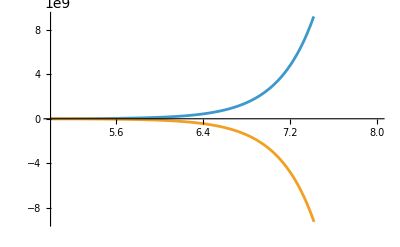

```mathematica
Plot[{ⅇ^t (-1+2 ⅇ^(2 t)),-ⅇ^t (1+2 ⅇ^(2 t))}, {t,5, 8}]
```